```mathematica
{o,y,x} = {{164.55263157894728,57.119298245614004},{164.55263157894728,491.3824561403509},{661.1315789473681,57.119298245614004}};
trans = FindGeometricTransform[{{0.94, 0.0}, { 0.94,0.2}, {1.,0}}, {o,y,x}][[2]]
```

TransformationFunction[(0.000120827 | 2.22206×10^-17 | 0.920118
6.88539×10^-17 | 0.00046055 | -0.0263063
0. | 0. | 1.)]

```mathematica
rawDat = {{455.6842105263158,202.1982456140351},{455.6842105263158,191.48771929824562},{455.6842105263158,184.6719298245614},{452.76315789473693,171.0403508771929},{453.73684210526307,161.30350877192978},{449.84210526315786,149.619298245614},{443.99999999999994,137.93508771929822},{438.15789473684214,126.25087719298244},{427.44736842105266,112.61929824561395},{420.6315789473684,104.82982456140348},{413.8157894736842,98.01403508771921},{407.9736842105263,93.14561403508759},{397.2631578947368,87.30350877192984},{366.1052631578946,71.72456140350874},{323.26315789473676,60.04035087719291},{292.1052631578948,56.1456140350877},{241.4736842105263,56.1456140350877},{221.02631578947359,56.1456140350877},{198.63157894736844,56.1456140350877},{165.5263157894737,56.1456140350877}};
```

```mathematica
dat = trans@rawDat
```

{{0.975176,0.0668161},{0.975176,0.0618834},{0.975176,0.0587444},{0.974824,0.0524664},{0.974941,0.0479821},{0.974471,0.0426009},{0.973765,0.0372197},{0.973059,0.0318386},{0.971765,0.0255605},{0.970941,0.0219731},{0.970118,0.0188341},{0.969412,0.0165919},{0.968118,0.0139013},{0.964353,0.00672646},{0.959176,0.00134529},{0.955412,-0.00044843},{0.949294,-0.00044843},{0.946824,-0.00044843},{0.944118,-0.00044843},{0.940118,-0.00044843}}

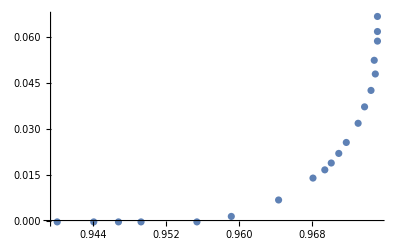

```mathematica
dat// ListPlot[#,Joined->False]&
```